# Project 1 - Convolution

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary INTE KLAR

For this project we had three sub-assignments. The three assignments built upon each other and are specified with

### Section.Subsection Summary sub-assignment 1

#### Description

This assignment is based on a dice game. There are five dice in the form of the Platonic solids (one die with 4 possible outcomes, one with 6, one with 8, one with 12, and one with 20). All dice are thrown at once, and if the sum of all dice are 10 or below, or 45 or higher, the player win a Teddy bear to bring home (each game costs 2 euro). We will:

Determine the exact probability function of the sum.

Determine the exact probability of winning the Teddy bear.

Determine the expected investment to win a Teddy.

Calculate the probability of winning at least once in twenty games.

#### Result

See section 2.1.

41/3840 . See section 2.2

187.317 euros. See section 2.3

0.193208. See Section 2.4

### Section.Subsection Summary sub-assignment 2

#### Description

This sub-assignment builds upon sub-assignment 1. Now are are playing for a car. The game has been modified to throw the five dice ten times, and if the sum of all dice S satisfies S≤200 or S≥350, you win a car. We will:

Determine the exact probability of winning the car.

Determine the expected investment to win a car.

#### Result

0.00118278, or 850900891349950659211944876745258211767259/719405003058931854978559698800738304000000000. See section 3.1.

211366, or 179851250764732963744639924700184576000000000000/850900891349950659211944876745258211767259. See section 3.2.

### Section.Subsection Summary sub-assignment 3

#### Description

For the third sub-assignment we will:

Determine the expectation values and standard deviations of the distributions in the Teddy and the car case..

Determine the probabilities of the Teddy prize and the car prize using the normal distribution.

#### Result

## Section. Winning a teddy

### Section.Subsection Probability function of the sum

#### Solution

To start off we defined the probability functions of the dice. Since the dice are perfect, all of the sides have the exact same probability of getting their face up, so we can define them as Discrete uniform distributions from 1 to the amount of faces the die has.

pf(k)=P(X=k)=Piecewise[{{1/m, 1≤k≤m}, {0, otherwise}}]

Then we performed Convolutions in order. First with die 1 and 2, then we took the result from that and convoluted it with die 3, and then 4 and lastly 5. This gave us the probability function of the sum.

#### Discussion

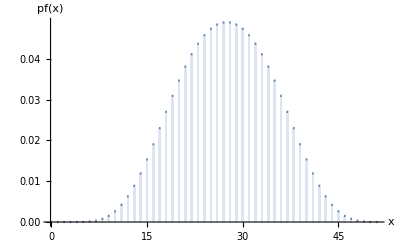

Above we have a diagram of the function

#### Code

```mathematica
ClearAll["`*"]
```

```mathematica
die1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
die2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
die3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
die4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
die5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[die1[y], die2[y], y, s];
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], die3[y], y, s];
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], die4[y], y, s];
pfResult[s_]= pfResult[s]=DiscreteConvolve[pf3[y], die5[y], y, s] ;(* pfResult is our function *)
```

```mathematica
Sum[pfResult[x], {x, 1, 50}] == 1
```

True

```mathematica
pfResult[5]
```

1/46080

```mathematica
pfResult[50]
```

1/46080

### Section.Subsection Exact probability to win Teddy

#### Solution

Now that we have the probability function of the sum of the dice, we can move on to calculate the probability of winning Teddy. We define the random variable S as the sum of the dice. We know that if S satisfies S≤10 or S≥45 you will win the Teddy. We can easily use that to calculate the probability.

P(X="winning teddy")= ∑_(k=5)^10 pf(k) +∑_(k=45)^50 pf(k)

We start at 5 because we know that it is the lowest possible outcome of the game, and stop at 50 because it is the highest.

#### Code

```mathematica
p = Sum[pfResult[x], {x, 5, 10}] + Sum[pfResult[x], {x, 45, 50}]
```

41/3840

### Section.Subsection Expected investment to win Teddy

#### Solution

To calculate the expected investment we need to to know how many times we are expected to play before winning. We know that calculating the expected value for a random variable that is distributed for finding the first successful event can be done like this.

μ= 1/p

Where p is the probability of  a successful outcome.

Now we only have to have to multiply the times we are expected to play with the cost (2 euros).

μ×2

#### Code

```mathematica
μ = N[(1 / p)*2] (* Smaller than in the explanation *)
```

187.317

### Section.Subsection Probability of winning Teddy in twenty games

#### Solution

We used binomial distribution to calculate the probability of winning Teddy after 20 games. We know that binomial distribution is used to calculate the probability of the random variable X which is defined as the amount of successful outcomes, while the probability of a successful outcome p, and the amount of tries n, is already defined.

pf(k)=P(X=k)=Piecewise[{{Binomial[n, k](p^k(1-p))^(n-k), 0≤k≤n}}]

#### Discussion

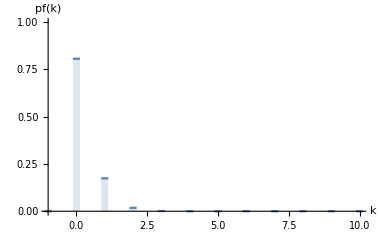

Here is a diagram of the binomial distribution function. It seems to coincide with our result (which is close 0.2). Here we can see that the chance of winning 0 times after 20 games is a little above 0.8.

#### Code

```mathematica
b := BinomialDistribution[20, p]
```

```mathematica
N[1 - PDF[b, 0]] (* The sum of all outcomes, subtracted by the chance of getting 0 wins *)
```

0.193208

## Section. Winning an electric car

### Section.Subsection Exact probability to win car

#### Solution

Here is a diagram of the binomial distribution function. It seems to coincide with our result (which is close 0.2). Here we can see that the chance of winning 0 times after 20 games is a little above 0.8.

#### Code

```mathematica
ClearAll["`*"]
```

```mathematica
die1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
die2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
die3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
die4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
die5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[die1[y], die2[y], y, s];
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], die3[y], y, s];
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], die4[y], y, s];
pf4[s_]= pfResult[s]=DiscreteConvolve[pf3[y], die5[y], y, s] ;
```

```mathematica
ct = Table[pf4[k], {k, 0, 50}];
ct2 = ListConvolve[ct, ct, {1, -1}, 0];
ct3 = ListConvolve[ct2, ct, {1, -1}, 0];
ct4 = ListConvolve[ct3, ct, {1, -1}, 0];
ct5 = ListConvolve[ct4, ct, {1, -1}, 0];
ct6 = ListConvolve[ct5, ct, {1, -1}, 0];
ct7 = ListConvolve[ct6, ct, {1, -1}, 0];
ct8 = ListConvolve[ct7, ct, {1, -1}, 0];
ct9 = ListConvolve[ct8, ct, {1, -1}, 0];
ct10 = ListConvolve[ct9, ct, {1, -1}, 0];
```

```mathematica
p = Sum[ct10[[x]], {x, 51, 201}] + Sum[ct10[[x]], {x, 351, 501}]
```

Part::partd: Part specification KonvTable10⟦51⟧ is longer than depth of object.

Part::partd: Part specification KonvTable10⟦52⟧ is longer than depth of object.

Part::partd: Part specification KonvTable10⟦53⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

KonvTable10⟦51⟧+KonvTable10⟦52⟧+KonvTable10⟦53⟧+KonvTable10⟦54⟧+KonvTable10⟦55⟧+KonvTable10⟦56⟧+KonvTable10⟦57⟧+KonvTable10⟦58⟧+KonvTable10⟦59⟧+KonvTable10⟦60⟧+KonvTable10⟦61⟧+KonvTable10⟦62⟧+KonvTable10⟦63⟧+KonvTable10⟦64⟧+KonvTable10⟦65⟧+KonvTable10⟦66⟧+KonvTable10⟦67⟧+KonvTable10⟦68⟧+KonvTable10⟦69⟧+KonvTable10⟦70⟧+KonvTable10⟦71⟧+KonvTable10⟦72⟧+KonvTable10⟦73⟧+KonvTable10⟦74⟧+KonvTable10⟦75⟧+KonvTable10⟦76⟧+KonvTable10⟦77⟧+KonvTable10⟦78⟧+KonvTable10⟦79⟧+KonvTable10⟦80⟧+KonvTable10⟦81⟧+KonvTable10⟦82⟧+KonvTable10⟦83⟧+KonvTable10⟦84⟧+KonvTable10⟦85⟧+KonvTable10⟦86⟧+KonvTable10⟦87⟧+KonvTable10⟦88⟧+KonvTable10⟦89⟧+KonvTable10⟦90⟧+KonvTable10⟦91⟧+KonvTable10⟦92⟧+KonvTable10⟦93⟧+KonvTable10⟦94⟧+KonvTable10⟦95⟧+KonvTable10⟦96⟧+KonvTable10⟦97⟧+KonvTable10⟦98⟧+KonvTable10⟦99⟧+KonvTable10⟦100⟧+KonvTable10⟦101⟧+KonvTable10⟦102⟧+KonvTable10⟦103⟧+KonvTable10⟦104⟧+KonvTable10⟦105⟧+KonvTable10⟦106⟧+KonvTable10⟦107⟧+KonvTable10⟦108⟧+KonvTable10⟦109⟧+KonvTable10⟦110⟧+KonvTable10⟦111⟧+KonvTable10⟦112⟧+KonvTable10⟦113⟧+KonvTable10⟦114⟧+KonvTable10⟦115⟧+KonvTable10⟦116⟧+KonvTable10⟦117⟧+KonvTable10⟦118⟧+KonvTable10⟦119⟧+KonvTable10⟦120⟧+KonvTable10⟦121⟧+KonvTable10⟦122⟧+KonvTable10⟦123⟧+KonvTable10⟦124⟧+KonvTable10⟦125⟧+KonvTable10⟦126⟧+KonvTable10⟦127⟧+KonvTable10⟦128⟧+KonvTable10⟦129⟧+KonvTable10⟦130⟧+KonvTable10⟦131⟧+KonvTable10⟦132⟧+KonvTable10⟦133⟧+KonvTable10⟦134⟧+KonvTable10⟦135⟧+KonvTable10⟦136⟧+KonvTable10⟦137⟧+KonvTable10⟦138⟧+KonvTable10⟦139⟧+KonvTable10⟦140⟧+KonvTable10⟦141⟧+KonvTable10⟦142⟧+KonvTable10⟦143⟧+KonvTable10⟦144⟧+KonvTable10⟦145⟧+KonvTable10⟦146⟧+KonvTable10⟦147⟧+KonvTable10⟦148⟧+KonvTable10⟦149⟧+KonvTable10⟦150⟧+KonvTable10⟦151⟧+KonvTable10⟦152⟧+KonvTable10⟦153⟧+KonvTable10⟦154⟧+KonvTable10⟦155⟧+KonvTable10⟦156⟧+KonvTable10⟦157⟧+KonvTable10⟦158⟧+KonvTable10⟦159⟧+KonvTable10⟦160⟧+KonvTable10⟦161⟧+KonvTable10⟦162⟧+KonvTable10⟦163⟧+KonvTable10⟦164⟧+KonvTable10⟦165⟧+KonvTable10⟦166⟧+KonvTable10⟦167⟧+KonvTable10⟦168⟧+KonvTable10⟦169⟧+KonvTable10⟦170⟧+KonvTable10⟦171⟧+KonvTable10⟦172⟧+KonvTable10⟦173⟧+KonvTable10⟦174⟧+KonvTable10⟦175⟧+KonvTable10⟦176⟧+KonvTable10⟦177⟧+KonvTable10⟦178⟧+KonvTable10⟦179⟧+KonvTable10⟦180⟧+KonvTable10⟦181⟧+KonvTable10⟦182⟧+KonvTable10⟦183⟧+KonvTable10⟦184⟧+KonvTable10⟦185⟧+KonvTable10⟦186⟧+KonvTable10⟦187⟧+KonvTable10⟦188⟧+KonvTable10⟦189⟧+KonvTable10⟦190⟧+KonvTable10⟦191⟧+KonvTable10⟦192⟧+KonvTable10⟦193⟧+KonvTable10⟦194⟧+KonvTable10⟦195⟧+KonvTable10⟦196⟧+KonvTable10⟦197⟧+KonvTable10⟦198⟧+KonvTable10⟦199⟧+KonvTable10⟦200⟧+KonvTable10⟦201⟧+KonvTable10⟦351⟧+KonvTable10⟦352⟧+KonvTable10⟦353⟧+KonvTable10⟦354⟧+KonvTable10⟦355⟧+KonvTable10⟦356⟧+KonvTable10⟦357⟧+KonvTable10⟦358⟧+KonvTable10⟦359⟧+KonvTable10⟦360⟧+KonvTable10⟦361⟧+KonvTable10⟦362⟧+KonvTable10⟦363⟧+KonvTable10⟦364⟧+KonvTable10⟦365⟧+KonvTable10⟦366⟧+KonvTable10⟦367⟧+KonvTable10⟦368⟧+KonvTable10⟦369⟧+KonvTable10⟦370⟧+KonvTable10⟦371⟧+KonvTable10⟦372⟧+KonvTable10⟦373⟧+KonvTable10⟦374⟧+KonvTable10⟦375⟧+KonvTable10⟦376⟧+KonvTable10⟦377⟧+KonvTable10⟦378⟧+KonvTable10⟦379⟧+KonvTable10⟦380⟧+KonvTable10⟦381⟧+KonvTable10⟦382⟧+KonvTable10⟦383⟧+KonvTable10⟦384⟧+KonvTable10⟦385⟧+KonvTable10⟦386⟧+KonvTable10⟦387⟧+KonvTable10⟦388⟧+KonvTable10⟦389⟧+KonvTable10⟦390⟧+KonvTable10⟦391⟧+KonvTable10⟦392⟧+KonvTable10⟦393⟧+KonvTable10⟦394⟧+KonvTable10⟦395⟧+KonvTable10⟦396⟧+KonvTable10⟦397⟧+KonvTable10⟦398⟧+KonvTable10⟦399⟧+KonvTable10⟦400⟧+KonvTable10⟦401⟧+KonvTable10⟦402⟧+KonvTable10⟦403⟧+KonvTable10⟦404⟧+KonvTable10⟦405⟧+KonvTable10⟦406⟧+KonvTable10⟦407⟧+KonvTable10⟦408⟧+KonvTable10⟦409⟧+KonvTable10⟦410⟧+KonvTable10⟦411⟧+KonvTable10⟦412⟧+KonvTable10⟦413⟧+KonvTable10⟦414⟧+KonvTable10⟦415⟧+KonvTable10⟦416⟧+KonvTable10⟦417⟧+KonvTable10⟦418⟧+KonvTable10⟦419⟧+KonvTable10⟦420⟧+KonvTable10⟦421⟧+KonvTable10⟦422⟧+KonvTable10⟦423⟧+KonvTable10⟦424⟧+KonvTable10⟦425⟧+KonvTable10⟦426⟧+KonvTable10⟦427⟧+KonvTable10⟦428⟧+KonvTable10⟦429⟧+KonvTable10⟦430⟧+KonvTable10⟦431⟧+KonvTable10⟦432⟧+KonvTable10⟦433⟧+KonvTable10⟦434⟧+KonvTable10⟦435⟧+KonvTable10⟦436⟧+KonvTable10⟦437⟧+KonvTable10⟦438⟧+KonvTable10⟦439⟧+KonvTable10⟦440⟧+KonvTable10⟦441⟧+KonvTable10⟦442⟧+KonvTable10⟦443⟧+KonvTable10⟦444⟧+KonvTable10⟦445⟧+KonvTable10⟦446⟧+KonvTable10⟦447⟧+KonvTable10⟦448⟧+KonvTable10⟦449⟧+KonvTable10⟦450⟧+KonvTable10⟦451⟧+KonvTable10⟦452⟧+KonvTable10⟦453⟧+KonvTable10⟦454⟧+KonvTable10⟦455⟧+KonvTable10⟦456⟧+KonvTable10⟦457⟧+KonvTable10⟦458⟧+KonvTable10⟦459⟧+KonvTable10⟦460⟧+KonvTable10⟦461⟧+KonvTable10⟦462⟧+KonvTable10⟦463⟧+KonvTable10⟦464⟧+KonvTable10⟦465⟧+KonvTable10⟦466⟧+KonvTable10⟦467⟧+KonvTable10⟦468⟧+KonvTable10⟦469⟧+KonvTable10⟦470⟧+KonvTable10⟦471⟧+KonvTable10⟦472⟧+KonvTable10⟦473⟧+KonvTable10⟦474⟧+KonvTable10⟦475⟧+KonvTable10⟦476⟧+KonvTable10⟦477⟧+KonvTable10⟦478⟧+KonvTable10⟦479⟧+KonvTable10⟦480⟧+KonvTable10⟦481⟧+KonvTable10⟦482⟧+KonvTable10⟦483⟧+KonvTable10⟦484⟧+KonvTable10⟦485⟧+KonvTable10⟦486⟧+KonvTable10⟦487⟧+KonvTable10⟦488⟧+KonvTable10⟦489⟧+KonvTable10⟦490⟧+KonvTable10⟦491⟧+KonvTable10⟦492⟧+KonvTable10⟦493⟧+KonvTable10⟦494⟧+KonvTable10⟦495⟧+KonvTable10⟦496⟧+KonvTable10⟦497⟧+KonvTable10⟦498⟧+KonvTable10⟦499⟧+KonvTable10⟦500⟧+KonvTable10⟦501⟧

```mathematica
N[p]
```

KonvTable10⟦51⟧+KonvTable10⟦52⟧+KonvTable10⟦53⟧+KonvTable10⟦54⟧+KonvTable10⟦55⟧+KonvTable10⟦56⟧+KonvTable10⟦57⟧+KonvTable10⟦58⟧+KonvTable10⟦59⟧+KonvTable10⟦60⟧+KonvTable10⟦61⟧+KonvTable10⟦62⟧+KonvTable10⟦63⟧+KonvTable10⟦64⟧+KonvTable10⟦65⟧+KonvTable10⟦66⟧+KonvTable10⟦67⟧+KonvTable10⟦68⟧+KonvTable10⟦69⟧+KonvTable10⟦70⟧+KonvTable10⟦71⟧+KonvTable10⟦72⟧+KonvTable10⟦73⟧+KonvTable10⟦74⟧+KonvTable10⟦75⟧+KonvTable10⟦76⟧+KonvTable10⟦77⟧+KonvTable10⟦78⟧+KonvTable10⟦79⟧+KonvTable10⟦80⟧+KonvTable10⟦81⟧+KonvTable10⟦82⟧+KonvTable10⟦83⟧+KonvTable10⟦84⟧+KonvTable10⟦85⟧+KonvTable10⟦86⟧+KonvTable10⟦87⟧+KonvTable10⟦88⟧+KonvTable10⟦89⟧+KonvTable10⟦90⟧+KonvTable10⟦91⟧+KonvTable10⟦92⟧+KonvTable10⟦93⟧+KonvTable10⟦94⟧+KonvTable10⟦95⟧+KonvTable10⟦96⟧+KonvTable10⟦97⟧+KonvTable10⟦98⟧+KonvTable10⟦99⟧+KonvTable10⟦100⟧+KonvTable10⟦101⟧+KonvTable10⟦102⟧+KonvTable10⟦103⟧+KonvTable10⟦104⟧+KonvTable10⟦105⟧+KonvTable10⟦106⟧+KonvTable10⟦107⟧+KonvTable10⟦108⟧+KonvTable10⟦109⟧+KonvTable10⟦110⟧+KonvTable10⟦111⟧+KonvTable10⟦112⟧+KonvTable10⟦113⟧+KonvTable10⟦114⟧+KonvTable10⟦115⟧+KonvTable10⟦116⟧+KonvTable10⟦117⟧+KonvTable10⟦118⟧+KonvTable10⟦119⟧+KonvTable10⟦120⟧+KonvTable10⟦121⟧+KonvTable10⟦122⟧+KonvTable10⟦123⟧+KonvTable10⟦124⟧+KonvTable10⟦125⟧+KonvTable10⟦126⟧+KonvTable10⟦127⟧+KonvTable10⟦128⟧+KonvTable10⟦129⟧+KonvTable10⟦130⟧+KonvTable10⟦131⟧+KonvTable10⟦132⟧+KonvTable10⟦133⟧+KonvTable10⟦134⟧+KonvTable10⟦135⟧+KonvTable10⟦136⟧+KonvTable10⟦137⟧+KonvTable10⟦138⟧+KonvTable10⟦139⟧+KonvTable10⟦140⟧+KonvTable10⟦141⟧+KonvTable10⟦142⟧+KonvTable10⟦143⟧+KonvTable10⟦144⟧+KonvTable10⟦145⟧+KonvTable10⟦146⟧+KonvTable10⟦147⟧+KonvTable10⟦148⟧+KonvTable10⟦149⟧+KonvTable10⟦150⟧+KonvTable10⟦151⟧+KonvTable10⟦152⟧+KonvTable10⟦153⟧+KonvTable10⟦154⟧+KonvTable10⟦155⟧+KonvTable10⟦156⟧+KonvTable10⟦157⟧+KonvTable10⟦158⟧+KonvTable10⟦159⟧+KonvTable10⟦160⟧+KonvTable10⟦161⟧+KonvTable10⟦162⟧+KonvTable10⟦163⟧+KonvTable10⟦164⟧+KonvTable10⟦165⟧+KonvTable10⟦166⟧+KonvTable10⟦167⟧+KonvTable10⟦168⟧+KonvTable10⟦169⟧+KonvTable10⟦170⟧+KonvTable10⟦171⟧+KonvTable10⟦172⟧+KonvTable10⟦173⟧+KonvTable10⟦174⟧+KonvTable10⟦175⟧+KonvTable10⟦176⟧+KonvTable10⟦177⟧+KonvTable10⟦178⟧+KonvTable10⟦179⟧+KonvTable10⟦180⟧+KonvTable10⟦181⟧+KonvTable10⟦182⟧+KonvTable10⟦183⟧+KonvTable10⟦184⟧+KonvTable10⟦185⟧+KonvTable10⟦186⟧+KonvTable10⟦187⟧+KonvTable10⟦188⟧+KonvTable10⟦189⟧+KonvTable10⟦190⟧+KonvTable10⟦191⟧+KonvTable10⟦192⟧+KonvTable10⟦193⟧+KonvTable10⟦194⟧+KonvTable10⟦195⟧+KonvTable10⟦196⟧+KonvTable10⟦197⟧+KonvTable10⟦198⟧+KonvTable10⟦199⟧+KonvTable10⟦200⟧+KonvTable10⟦201⟧+KonvTable10⟦351⟧+KonvTable10⟦352⟧+KonvTable10⟦353⟧+KonvTable10⟦354⟧+KonvTable10⟦355⟧+KonvTable10⟦356⟧+KonvTable10⟦357⟧+KonvTable10⟦358⟧+KonvTable10⟦359⟧+KonvTable10⟦360⟧+KonvTable10⟦361⟧+KonvTable10⟦362⟧+KonvTable10⟦363⟧+KonvTable10⟦364⟧+KonvTable10⟦365⟧+KonvTable10⟦366⟧+KonvTable10⟦367⟧+KonvTable10⟦368⟧+KonvTable10⟦369⟧+KonvTable10⟦370⟧+KonvTable10⟦371⟧+KonvTable10⟦372⟧+KonvTable10⟦373⟧+KonvTable10⟦374⟧+KonvTable10⟦375⟧+KonvTable10⟦376⟧+KonvTable10⟦377⟧+KonvTable10⟦378⟧+KonvTable10⟦379⟧+KonvTable10⟦380⟧+KonvTable10⟦381⟧+KonvTable10⟦382⟧+KonvTable10⟦383⟧+KonvTable10⟦384⟧+KonvTable10⟦385⟧+KonvTable10⟦386⟧+KonvTable10⟦387⟧+KonvTable10⟦388⟧+KonvTable10⟦389⟧+KonvTable10⟦390⟧+KonvTable10⟦391⟧+KonvTable10⟦392⟧+KonvTable10⟦393⟧+KonvTable10⟦394⟧+KonvTable10⟦395⟧+KonvTable10⟦396⟧+KonvTable10⟦397⟧+KonvTable10⟦398⟧+KonvTable10⟦399⟧+KonvTable10⟦400⟧+KonvTable10⟦401⟧+KonvTable10⟦402⟧+KonvTable10⟦403⟧+KonvTable10⟦404⟧+KonvTable10⟦405⟧+KonvTable10⟦406⟧+KonvTable10⟦407⟧+KonvTable10⟦408⟧+KonvTable10⟦409⟧+KonvTable10⟦410⟧+KonvTable10⟦411⟧+KonvTable10⟦412⟧+KonvTable10⟦413⟧+KonvTable10⟦414⟧+KonvTable10⟦415⟧+KonvTable10⟦416⟧+KonvTable10⟦417⟧+KonvTable10⟦418⟧+KonvTable10⟦419⟧+KonvTable10⟦420⟧+KonvTable10⟦421⟧+KonvTable10⟦422⟧+KonvTable10⟦423⟧+KonvTable10⟦424⟧+KonvTable10⟦425⟧+KonvTable10⟦426⟧+KonvTable10⟦427⟧+KonvTable10⟦428⟧+KonvTable10⟦429⟧+KonvTable10⟦430⟧+KonvTable10⟦431⟧+KonvTable10⟦432⟧+KonvTable10⟦433⟧+KonvTable10⟦434⟧+KonvTable10⟦435⟧+KonvTable10⟦436⟧+KonvTable10⟦437⟧+KonvTable10⟦438⟧+KonvTable10⟦439⟧+KonvTable10⟦440⟧+KonvTable10⟦441⟧+KonvTable10⟦442⟧+KonvTable10⟦443⟧+KonvTable10⟦444⟧+KonvTable10⟦445⟧+KonvTable10⟦446⟧+KonvTable10⟦447⟧+KonvTable10⟦448⟧+KonvTable10⟦449⟧+KonvTable10⟦450⟧+KonvTable10⟦451⟧+KonvTable10⟦452⟧+KonvTable10⟦453⟧+KonvTable10⟦454⟧+KonvTable10⟦455⟧+KonvTable10⟦456⟧+KonvTable10⟦457⟧+KonvTable10⟦458⟧+KonvTable10⟦459⟧+KonvTable10⟦460⟧+KonvTable10⟦461⟧+KonvTable10⟦462⟧+KonvTable10⟦463⟧+KonvTable10⟦464⟧+KonvTable10⟦465⟧+KonvTable10⟦466⟧+KonvTable10⟦467⟧+KonvTable10⟦468⟧+KonvTable10⟦469⟧+KonvTable10⟦470⟧+KonvTable10⟦471⟧+KonvTable10⟦472⟧+KonvTable10⟦473⟧+KonvTable10⟦474⟧+KonvTable10⟦475⟧+KonvTable10⟦476⟧+KonvTable10⟦477⟧+KonvTable10⟦478⟧+KonvTable10⟦479⟧+KonvTable10⟦480⟧+KonvTable10⟦481⟧+KonvTable10⟦482⟧+KonvTable10⟦483⟧+KonvTable10⟦484⟧+KonvTable10⟦485⟧+KonvTable10⟦486⟧+KonvTable10⟦487⟧+KonvTable10⟦488⟧+KonvTable10⟦489⟧+KonvTable10⟦490⟧+KonvTable10⟦491⟧+KonvTable10⟦492⟧+KonvTable10⟦493⟧+KonvTable10⟦494⟧+KonvTable10⟦495⟧+KonvTable10⟦496⟧+KonvTable10⟦497⟧+KonvTable10⟦498⟧+KonvTable10⟦499⟧+KonvTable10⟦500⟧+KonvTable10⟦501⟧

### Section.Subsection Expected investment to win car

#### Solution

This is done the same way as in section 2.3. We used to following formula

μ= 1/p

Which is the expected amount of tries before winning.

Now we only have to have to multiply the times we are expected to play with the cost (250 euros).

μ×250

#### Code

```mathematica
(1/p)*250 (* Smaller than in the explanation *)
```

250/(KonvTable10⟦51⟧+KonvTable10⟦52⟧+KonvTable10⟦53⟧+KonvTable10⟦54⟧+KonvTable10⟦55⟧+KonvTable10⟦56⟧+KonvTable10⟦57⟧+KonvTable10⟦58⟧+KonvTable10⟦59⟧+KonvTable10⟦60⟧+KonvTable10⟦61⟧+KonvTable10⟦62⟧+KonvTable10⟦63⟧+KonvTable10⟦64⟧+KonvTable10⟦65⟧+KonvTable10⟦66⟧+KonvTable10⟦67⟧+KonvTable10⟦68⟧+KonvTable10⟦69⟧+KonvTable10⟦70⟧+KonvTable10⟦71⟧+KonvTable10⟦72⟧+KonvTable10⟦73⟧+KonvTable10⟦74⟧+KonvTable10⟦75⟧+KonvTable10⟦76⟧+KonvTable10⟦77⟧+KonvTable10⟦78⟧+KonvTable10⟦79⟧+KonvTable10⟦80⟧+KonvTable10⟦81⟧+KonvTable10⟦82⟧+KonvTable10⟦83⟧+KonvTable10⟦84⟧+KonvTable10⟦85⟧+KonvTable10⟦86⟧+KonvTable10⟦87⟧+KonvTable10⟦88⟧+KonvTable10⟦89⟧+KonvTable10⟦90⟧+KonvTable10⟦91⟧+KonvTable10⟦92⟧+KonvTable10⟦93⟧+KonvTable10⟦94⟧+KonvTable10⟦95⟧+KonvTable10⟦96⟧+KonvTable10⟦97⟧+KonvTable10⟦98⟧+KonvTable10⟦99⟧+KonvTable10⟦100⟧+KonvTable10⟦101⟧+KonvTable10⟦102⟧+KonvTable10⟦103⟧+KonvTable10⟦104⟧+KonvTable10⟦105⟧+KonvTable10⟦106⟧+KonvTable10⟦107⟧+KonvTable10⟦108⟧+KonvTable10⟦109⟧+KonvTable10⟦110⟧+KonvTable10⟦111⟧+KonvTable10⟦112⟧+KonvTable10⟦113⟧+KonvTable10⟦114⟧+KonvTable10⟦115⟧+KonvTable10⟦116⟧+KonvTable10⟦117⟧+KonvTable10⟦118⟧+KonvTable10⟦119⟧+KonvTable10⟦120⟧+KonvTable10⟦121⟧+KonvTable10⟦122⟧+KonvTable10⟦123⟧+KonvTable10⟦124⟧+KonvTable10⟦125⟧+KonvTable10⟦126⟧+KonvTable10⟦127⟧+KonvTable10⟦128⟧+KonvTable10⟦129⟧+KonvTable10⟦130⟧+KonvTable10⟦131⟧+KonvTable10⟦132⟧+KonvTable10⟦133⟧+KonvTable10⟦134⟧+KonvTable10⟦135⟧+KonvTable10⟦136⟧+KonvTable10⟦137⟧+KonvTable10⟦138⟧+KonvTable10⟦139⟧+KonvTable10⟦140⟧+KonvTable10⟦141⟧+KonvTable10⟦142⟧+KonvTable10⟦143⟧+KonvTable10⟦144⟧+KonvTable10⟦145⟧+KonvTable10⟦146⟧+KonvTable10⟦147⟧+KonvTable10⟦148⟧+KonvTable10⟦149⟧+KonvTable10⟦150⟧+KonvTable10⟦151⟧+KonvTable10⟦152⟧+KonvTable10⟦153⟧+KonvTable10⟦154⟧+KonvTable10⟦155⟧+KonvTable10⟦156⟧+KonvTable10⟦157⟧+KonvTable10⟦158⟧+KonvTable10⟦159⟧+KonvTable10⟦160⟧+KonvTable10⟦161⟧+KonvTable10⟦162⟧+KonvTable10⟦163⟧+KonvTable10⟦164⟧+KonvTable10⟦165⟧+KonvTable10⟦166⟧+KonvTable10⟦167⟧+KonvTable10⟦168⟧+KonvTable10⟦169⟧+KonvTable10⟦170⟧+KonvTable10⟦171⟧+KonvTable10⟦172⟧+KonvTable10⟦173⟧+KonvTable10⟦174⟧+KonvTable10⟦175⟧+KonvTable10⟦176⟧+KonvTable10⟦177⟧+KonvTable10⟦178⟧+KonvTable10⟦179⟧+KonvTable10⟦180⟧+KonvTable10⟦181⟧+KonvTable10⟦182⟧+KonvTable10⟦183⟧+KonvTable10⟦184⟧+KonvTable10⟦185⟧+KonvTable10⟦186⟧+KonvTable10⟦187⟧+KonvTable10⟦188⟧+KonvTable10⟦189⟧+KonvTable10⟦190⟧+KonvTable10⟦191⟧+KonvTable10⟦192⟧+KonvTable10⟦193⟧+KonvTable10⟦194⟧+KonvTable10⟦195⟧+KonvTable10⟦196⟧+KonvTable10⟦197⟧+KonvTable10⟦198⟧+KonvTable10⟦199⟧+KonvTable10⟦200⟧+KonvTable10⟦201⟧+KonvTable10⟦351⟧+KonvTable10⟦352⟧+KonvTable10⟦353⟧+KonvTable10⟦354⟧+KonvTable10⟦355⟧+KonvTable10⟦356⟧+KonvTable10⟦357⟧+KonvTable10⟦358⟧+KonvTable10⟦359⟧+KonvTable10⟦360⟧+KonvTable10⟦361⟧+KonvTable10⟦362⟧+KonvTable10⟦363⟧+KonvTable10⟦364⟧+KonvTable10⟦365⟧+KonvTable10⟦366⟧+KonvTable10⟦367⟧+KonvTable10⟦368⟧+KonvTable10⟦369⟧+KonvTable10⟦370⟧+KonvTable10⟦371⟧+KonvTable10⟦372⟧+KonvTable10⟦373⟧+KonvTable10⟦374⟧+KonvTable10⟦375⟧+KonvTable10⟦376⟧+KonvTable10⟦377⟧+KonvTable10⟦378⟧+KonvTable10⟦379⟧+KonvTable10⟦380⟧+KonvTable10⟦381⟧+KonvTable10⟦382⟧+KonvTable10⟦383⟧+KonvTable10⟦384⟧+KonvTable10⟦385⟧+KonvTable10⟦386⟧+KonvTable10⟦387⟧+KonvTable10⟦388⟧+KonvTable10⟦389⟧+KonvTable10⟦390⟧+KonvTable10⟦391⟧+KonvTable10⟦392⟧+KonvTable10⟦393⟧+KonvTable10⟦394⟧+KonvTable10⟦395⟧+KonvTable10⟦396⟧+KonvTable10⟦397⟧+KonvTable10⟦398⟧+KonvTable10⟦399⟧+KonvTable10⟦400⟧+KonvTable10⟦401⟧+KonvTable10⟦402⟧+KonvTable10⟦403⟧+KonvTable10⟦404⟧+KonvTable10⟦405⟧+KonvTable10⟦406⟧+KonvTable10⟦407⟧+KonvTable10⟦408⟧+KonvTable10⟦409⟧+KonvTable10⟦410⟧+KonvTable10⟦411⟧+KonvTable10⟦412⟧+KonvTable10⟦413⟧+KonvTable10⟦414⟧+KonvTable10⟦415⟧+KonvTable10⟦416⟧+KonvTable10⟦417⟧+KonvTable10⟦418⟧+KonvTable10⟦419⟧+KonvTable10⟦420⟧+KonvTable10⟦421⟧+KonvTable10⟦422⟧+KonvTable10⟦423⟧+KonvTable10⟦424⟧+KonvTable10⟦425⟧+KonvTable10⟦426⟧+KonvTable10⟦427⟧+KonvTable10⟦428⟧+KonvTable10⟦429⟧+KonvTable10⟦430⟧+KonvTable10⟦431⟧+KonvTable10⟦432⟧+KonvTable10⟦433⟧+KonvTable10⟦434⟧+KonvTable10⟦435⟧+KonvTable10⟦436⟧+KonvTable10⟦437⟧+KonvTable10⟦438⟧+KonvTable10⟦439⟧+KonvTable10⟦440⟧+KonvTable10⟦441⟧+KonvTable10⟦442⟧+KonvTable10⟦443⟧+KonvTable10⟦444⟧+KonvTable10⟦445⟧+KonvTable10⟦446⟧+KonvTable10⟦447⟧+KonvTable10⟦448⟧+KonvTable10⟦449⟧+KonvTable10⟦450⟧+KonvTable10⟦451⟧+KonvTable10⟦452⟧+KonvTable10⟦453⟧+KonvTable10⟦454⟧+KonvTable10⟦455⟧+KonvTable10⟦456⟧+KonvTable10⟦457⟧+KonvTable10⟦458⟧+KonvTable10⟦459⟧+KonvTable10⟦460⟧+KonvTable10⟦461⟧+KonvTable10⟦462⟧+KonvTable10⟦463⟧+KonvTable10⟦464⟧+KonvTable10⟦465⟧+KonvTable10⟦466⟧+KonvTable10⟦467⟧+KonvTable10⟦468⟧+KonvTable10⟦469⟧+KonvTable10⟦470⟧+KonvTable10⟦471⟧+KonvTable10⟦472⟧+KonvTable10⟦473⟧+KonvTable10⟦474⟧+KonvTable10⟦475⟧+KonvTable10⟦476⟧+KonvTable10⟦477⟧+KonvTable10⟦478⟧+KonvTable10⟦479⟧+KonvTable10⟦480⟧+KonvTable10⟦481⟧+KonvTable10⟦482⟧+KonvTable10⟦483⟧+KonvTable10⟦484⟧+KonvTable10⟦485⟧+KonvTable10⟦486⟧+KonvTable10⟦487⟧+KonvTable10⟦488⟧+KonvTable10⟦489⟧+KonvTable10⟦490⟧+KonvTable10⟦491⟧+KonvTable10⟦492⟧+KonvTable10⟦493⟧+KonvTable10⟦494⟧+KonvTable10⟦495⟧+KonvTable10⟦496⟧+KonvTable10⟦497⟧+KonvTable10⟦498⟧+KonvTable10⟦499⟧+KonvTable10⟦500⟧+KonvTable10⟦501⟧)

```mathematica
N[(1/p)*250]
```

250./(KonvTable10⟦51⟧+KonvTable10⟦52⟧+KonvTable10⟦53⟧+KonvTable10⟦54⟧+KonvTable10⟦55⟧+KonvTable10⟦56⟧+KonvTable10⟦57⟧+KonvTable10⟦58⟧+KonvTable10⟦59⟧+KonvTable10⟦60⟧+KonvTable10⟦61⟧+KonvTable10⟦62⟧+KonvTable10⟦63⟧+KonvTable10⟦64⟧+KonvTable10⟦65⟧+KonvTable10⟦66⟧+KonvTable10⟦67⟧+KonvTable10⟦68⟧+KonvTable10⟦69⟧+KonvTable10⟦70⟧+KonvTable10⟦71⟧+KonvTable10⟦72⟧+KonvTable10⟦73⟧+KonvTable10⟦74⟧+KonvTable10⟦75⟧+KonvTable10⟦76⟧+KonvTable10⟦77⟧+KonvTable10⟦78⟧+KonvTable10⟦79⟧+KonvTable10⟦80⟧+KonvTable10⟦81⟧+KonvTable10⟦82⟧+KonvTable10⟦83⟧+KonvTable10⟦84⟧+KonvTable10⟦85⟧+KonvTable10⟦86⟧+KonvTable10⟦87⟧+KonvTable10⟦88⟧+KonvTable10⟦89⟧+KonvTable10⟦90⟧+KonvTable10⟦91⟧+KonvTable10⟦92⟧+KonvTable10⟦93⟧+KonvTable10⟦94⟧+KonvTable10⟦95⟧+KonvTable10⟦96⟧+KonvTable10⟦97⟧+KonvTable10⟦98⟧+KonvTable10⟦99⟧+KonvTable10⟦100⟧+KonvTable10⟦101⟧+KonvTable10⟦102⟧+KonvTable10⟦103⟧+KonvTable10⟦104⟧+KonvTable10⟦105⟧+KonvTable10⟦106⟧+KonvTable10⟦107⟧+KonvTable10⟦108⟧+KonvTable10⟦109⟧+KonvTable10⟦110⟧+KonvTable10⟦111⟧+KonvTable10⟦112⟧+KonvTable10⟦113⟧+KonvTable10⟦114⟧+KonvTable10⟦115⟧+KonvTable10⟦116⟧+KonvTable10⟦117⟧+KonvTable10⟦118⟧+KonvTable10⟦119⟧+KonvTable10⟦120⟧+KonvTable10⟦121⟧+KonvTable10⟦122⟧+KonvTable10⟦123⟧+KonvTable10⟦124⟧+KonvTable10⟦125⟧+KonvTable10⟦126⟧+KonvTable10⟦127⟧+KonvTable10⟦128⟧+KonvTable10⟦129⟧+KonvTable10⟦130⟧+KonvTable10⟦131⟧+KonvTable10⟦132⟧+KonvTable10⟦133⟧+KonvTable10⟦134⟧+KonvTable10⟦135⟧+KonvTable10⟦136⟧+KonvTable10⟦137⟧+KonvTable10⟦138⟧+KonvTable10⟦139⟧+KonvTable10⟦140⟧+KonvTable10⟦141⟧+KonvTable10⟦142⟧+KonvTable10⟦143⟧+KonvTable10⟦144⟧+KonvTable10⟦145⟧+KonvTable10⟦146⟧+KonvTable10⟦147⟧+KonvTable10⟦148⟧+KonvTable10⟦149⟧+KonvTable10⟦150⟧+KonvTable10⟦151⟧+KonvTable10⟦152⟧+KonvTable10⟦153⟧+KonvTable10⟦154⟧+KonvTable10⟦155⟧+KonvTable10⟦156⟧+KonvTable10⟦157⟧+KonvTable10⟦158⟧+KonvTable10⟦159⟧+KonvTable10⟦160⟧+KonvTable10⟦161⟧+KonvTable10⟦162⟧+KonvTable10⟦163⟧+KonvTable10⟦164⟧+KonvTable10⟦165⟧+KonvTable10⟦166⟧+KonvTable10⟦167⟧+KonvTable10⟦168⟧+KonvTable10⟦169⟧+KonvTable10⟦170⟧+KonvTable10⟦171⟧+KonvTable10⟦172⟧+KonvTable10⟦173⟧+KonvTable10⟦174⟧+KonvTable10⟦175⟧+KonvTable10⟦176⟧+KonvTable10⟦177⟧+KonvTable10⟦178⟧+KonvTable10⟦179⟧+KonvTable10⟦180⟧+KonvTable10⟦181⟧+KonvTable10⟦182⟧+KonvTable10⟦183⟧+KonvTable10⟦184⟧+KonvTable10⟦185⟧+KonvTable10⟦186⟧+KonvTable10⟦187⟧+KonvTable10⟦188⟧+KonvTable10⟦189⟧+KonvTable10⟦190⟧+KonvTable10⟦191⟧+KonvTable10⟦192⟧+KonvTable10⟦193⟧+KonvTable10⟦194⟧+KonvTable10⟦195⟧+KonvTable10⟦196⟧+KonvTable10⟦197⟧+KonvTable10⟦198⟧+KonvTable10⟦199⟧+KonvTable10⟦200⟧+KonvTable10⟦201⟧+KonvTable10⟦351⟧+KonvTable10⟦352⟧+KonvTable10⟦353⟧+KonvTable10⟦354⟧+KonvTable10⟦355⟧+KonvTable10⟦356⟧+KonvTable10⟦357⟧+KonvTable10⟦358⟧+KonvTable10⟦359⟧+KonvTable10⟦360⟧+KonvTable10⟦361⟧+KonvTable10⟦362⟧+KonvTable10⟦363⟧+KonvTable10⟦364⟧+KonvTable10⟦365⟧+KonvTable10⟦366⟧+KonvTable10⟦367⟧+KonvTable10⟦368⟧+KonvTable10⟦369⟧+KonvTable10⟦370⟧+KonvTable10⟦371⟧+KonvTable10⟦372⟧+KonvTable10⟦373⟧+KonvTable10⟦374⟧+KonvTable10⟦375⟧+KonvTable10⟦376⟧+KonvTable10⟦377⟧+KonvTable10⟦378⟧+KonvTable10⟦379⟧+KonvTable10⟦380⟧+KonvTable10⟦381⟧+KonvTable10⟦382⟧+KonvTable10⟦383⟧+KonvTable10⟦384⟧+KonvTable10⟦385⟧+KonvTable10⟦386⟧+KonvTable10⟦387⟧+KonvTable10⟦388⟧+KonvTable10⟦389⟧+KonvTable10⟦390⟧+KonvTable10⟦391⟧+KonvTable10⟦392⟧+KonvTable10⟦393⟧+KonvTable10⟦394⟧+KonvTable10⟦395⟧+KonvTable10⟦396⟧+KonvTable10⟦397⟧+KonvTable10⟦398⟧+KonvTable10⟦399⟧+KonvTable10⟦400⟧+KonvTable10⟦401⟧+KonvTable10⟦402⟧+KonvTable10⟦403⟧+KonvTable10⟦404⟧+KonvTable10⟦405⟧+KonvTable10⟦406⟧+KonvTable10⟦407⟧+KonvTable10⟦408⟧+KonvTable10⟦409⟧+KonvTable10⟦410⟧+KonvTable10⟦411⟧+KonvTable10⟦412⟧+KonvTable10⟦413⟧+KonvTable10⟦414⟧+KonvTable10⟦415⟧+KonvTable10⟦416⟧+KonvTable10⟦417⟧+KonvTable10⟦418⟧+KonvTable10⟦419⟧+KonvTable10⟦420⟧+KonvTable10⟦421⟧+KonvTable10⟦422⟧+KonvTable10⟦423⟧+KonvTable10⟦424⟧+KonvTable10⟦425⟧+KonvTable10⟦426⟧+KonvTable10⟦427⟧+KonvTable10⟦428⟧+KonvTable10⟦429⟧+KonvTable10⟦430⟧+KonvTable10⟦431⟧+KonvTable10⟦432⟧+KonvTable10⟦433⟧+KonvTable10⟦434⟧+KonvTable10⟦435⟧+KonvTable10⟦436⟧+KonvTable10⟦437⟧+KonvTable10⟦438⟧+KonvTable10⟦439⟧+KonvTable10⟦440⟧+KonvTable10⟦441⟧+KonvTable10⟦442⟧+KonvTable10⟦443⟧+KonvTable10⟦444⟧+KonvTable10⟦445⟧+KonvTable10⟦446⟧+KonvTable10⟦447⟧+KonvTable10⟦448⟧+KonvTable10⟦449⟧+KonvTable10⟦450⟧+KonvTable10⟦451⟧+KonvTable10⟦452⟧+KonvTable10⟦453⟧+KonvTable10⟦454⟧+KonvTable10⟦455⟧+KonvTable10⟦456⟧+KonvTable10⟦457⟧+KonvTable10⟦458⟧+KonvTable10⟦459⟧+KonvTable10⟦460⟧+KonvTable10⟦461⟧+KonvTable10⟦462⟧+KonvTable10⟦463⟧+KonvTable10⟦464⟧+KonvTable10⟦465⟧+KonvTable10⟦466⟧+KonvTable10⟦467⟧+KonvTable10⟦468⟧+KonvTable10⟦469⟧+KonvTable10⟦470⟧+KonvTable10⟦471⟧+KonvTable10⟦472⟧+KonvTable10⟦473⟧+KonvTable10⟦474⟧+KonvTable10⟦475⟧+KonvTable10⟦476⟧+KonvTable10⟦477⟧+KonvTable10⟦478⟧+KonvTable10⟦479⟧+KonvTable10⟦480⟧+KonvTable10⟦481⟧+KonvTable10⟦482⟧+KonvTable10⟦483⟧+KonvTable10⟦484⟧+KonvTable10⟦485⟧+KonvTable10⟦486⟧+KonvTable10⟦487⟧+KonvTable10⟦488⟧+KonvTable10⟦489⟧+KonvTable10⟦490⟧+KonvTable10⟦491⟧+KonvTable10⟦492⟧+KonvTable10⟦493⟧+KonvTable10⟦494⟧+KonvTable10⟦495⟧+KonvTable10⟦496⟧+KonvTable10⟦497⟧+KonvTable10⟦498⟧+KonvTable10⟦499⟧+KonvTable10⟦500⟧+KonvTable10⟦501⟧)

## Section. Normal distribution

### Section.Subsection The expectation values and standard deviations of the distributions in the Teddy and the car case

#### Solution

The formula for calculating the expected values for a discrete probability function is

μ=∑_(∀x) x pf(x)

And the formula for variance is

σ^2=(∑_(∀x) x^2 pf(x)) - μ^2

The formula for calculating the standard deviation is

σ = √(σ^2)

We simply used those formulas to implement our code.

#### Code

```mathematica
ClearAll["`*"]
```

```mathematica
die1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
die2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
die3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
die4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
die5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[die1[y], die2[y], y, s];
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], die3[y], y, s];
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], die4[y], y, s];
pf4[s_]= pfResult[s]=DiscreteConvolve[pf3[y], die5[y], y, s] ;
```

```mathematica
ct = Table[pf4[k], {k, 0, 50}];
ct2 = ListConvolve[ct, ct, {1, -1}, 0];
ct3 = ListConvolve[ct2, ct, {1, -1}, 0];
ct4 = ListConvolve[ct3, ct, {1, -1}, 0];
ct5 = ListConvolve[ct4, ct, {1, -1}, 0];
ct6 = ListConvolve[ct5, ct, {1, -1}, 0];
ct7 = ListConvolve[ct6, ct, {1, -1}, 0];
ct8 = ListConvolve[ct7, ct, {1, -1}, 0];
ct9 = ListConvolve[ct8, ct, {1, -1}, 0];
ct10 = ListConvolve[ct9, ct, {1, -1}, 0];
```

```mathematica
(* For the Teddy bear *)
```

```mathematica
μ1=Sum[x pf4[x],{x,5,50}]
```

55/2

```mathematica
σ1Power2= Sum[k^2 * pf4[k], {k, 5, 50}] -μ1^2
```

655/12

```mathematica
σ1= Sqrt[σ1Power2]
```

(√(655/3))/2

```mathematica
(* For the Car *)
```

```mathematica
μ2 = Sum[k*ct10[[k]], {k , 51, 501}]
```

276

```mathematica
σ2Power2 = Sum[k^2 * ct10[[k]], {k,51, 501}] - μ2^2
```

3275/6

```mathematica
σ2 = Sqrt[σ2Power2]
```

5 √(131/6)

### Section.Subsection The probabilities of the Teddy prize and the car prize using the normal distribution

#### Solution

The normal distribution can be calculated as follows:

φ(t) = (1/√(2π))ⅇ^(-t^2/2)

pdf(t)=(1/σ)×φ((t-μ)/σ)

But we used the Mathematica implementation

#### Code

```mathematica
(* For Teddy bear *)
```

```mathematica
𝒟1:= NormalDistribution[μ1, σ1]
```

```mathematica
NProbability[5 ≤ X ≤ 10 || 45 ≤ X ≤ 50, X \[Distributed] 𝒟1]
```

0.015528

```mathematica
(* For Car *)
```

```mathematica
𝒟2:= NormalDistribution[μ2, σ2]
```

```mathematica
NProbability[X ≤ 201 || X ≥ 351, X \[Distributed] 𝒟2]
```

0.00132646